Complex numbers (§7):

```mathematica
Quit[]
```

```mathematica
i^2
I^2
```

i^2

-1

```mathematica
z=2+3*I
```

2+3 ⅈ

```mathematica
z1=1-I
z2=3+4*I
z1+z2
z1-z2
z1*z2
z1/z2
z1^5
```

1-ⅈ

3+4 ⅈ

4+3 ⅈ

-2-5 ⅈ

7+ⅈ

-1/25-(7 ⅈ)/25

-4+4 ⅈ

```mathematica
Quit[]
```

```mathematica
Values[Solve[z^2+2*z+5==0,z]]
```

{{-1-2 ⅈ},{-1+2 ⅈ}}

```mathematica
Values[Solve[(2+I)*z+(3-I)==4,z]]
```

{{3/5+ⅈ/5}}

```mathematica
a=Re[3-5*I]
b=Im[3-5*I]
```

3

-5

```mathematica
r=Abs[2+I]
phi=Arg[2+I]
N[r]
N[phi]
```

√5

ArcTan[1/2]

2.23607

0.463648

```mathematica
AbsArg[2+I]
```

{√5,ArcTan[1/2]}

```mathematica
Conjugate[3+5*I]
```

3-5 ⅈ

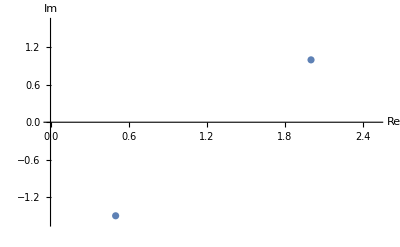

```mathematica
z={2+I,0.5-1.5*I};
ListPlot[Table[{Re[z[[k]]],Im[z[[k]]]},{k,1,2}],PlotRange->{{0,2.5},{-1.6,1.6}},AxesLabel->{"Re","Im"}]
```

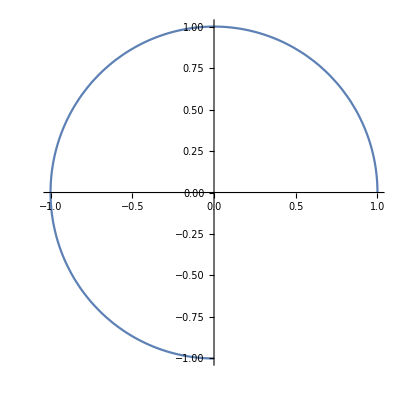

```mathematica
z=(Cos[Pi*t])+(Sin[(Pi*t)])*I;
ParametricPlot[{Re[z],Im[z]},{t,0,1.5}]
```